```mathematica
(* From http://mathematica.stackexchange.com/questions/13361/mollweide-maps-in-mathematica *)
ClearAll["Global`*"];
Needs["Misc`MapProjections`"];
SetDirectory[NotebookDirectory[]];
Directory[]
```

/Users/npadmana/myWork/npmma/Misc

```mathematica
?mapMollweide
```

mapMollweide[{lon, lat}, lon0:0] maps lat, lon (in radians by default) to (x,y) in the Mollweide coordinate system. 
   Note that {theta, phi} are assumed to be in a list. The central longitude is assumed to be 0, unless specified otherwise

```mathematica
?mapInverseMollweide
```

mapInverseMollweide[{x, y}, lon0:0] maps Mollweide coordinates x,y to lon, lat (in radians). 
    x,y must be in a list. The central longitude is assumed to be zero

```mathematica
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 15]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->15,PlotRangePadding->0,ColorFunction->colorFunction,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None}];
```

```mathematica
(* Now straight from the solution posted *)

grid0=With[{delta=Pi/36},Table[{lambda,phi},{phi,-Pi/2,Pi/2,delta},{lambda,-Pi,Pi,delta}]];
gr1=Graphics[{AbsoluteThickness[0.1],Line/@grid0,Line/@Transpose[grid0]},AspectRatio->1/2];
gr0=Flatten[{gr1[[1,2]][[Range[9]*4-1]],gr1[[1,3]][[Range[18]*4-3]]}]//Graphics[{AbsoluteThickness[0.4],#}]&;
grid=Show[{gr1,gr0},Axes->False];
grid=grid/.Line[pts_]:>{White,Line[(mapMollweide/@pts)]};
gr2=StreamPlot[{-1-Sin[x]^2+Sin[3y]+Cos[y]^2,1+Sin[2x]-Cos[y]^2},{x,-Pi,Pi},{y,-Pi/2,Pi/2},AspectRatio->1/2,Frame->False,StreamColorFunction->"ThermometerColors",StreamPoints->250];
gr2=gr2/.Arrow[pts_]:>Arrow[(mapMollweide/@pts)]/.Point[pts_]:>Point[mapMollweide[pts]]//Show[#,PlotRange->{{-2,2},{-1,1}}]&;
img=With[{img=Import["2ZPBK.jpg"]},ImageTransformation[img,mapInverseMollweide,{512,256}*4,DataRange->{{-Pi,Pi},{-Pi/2,Pi/2}},PlotRange->{{-2,2},{-1,1}},Padding->White]];
```

```mathematica
(* Plot the intermediate results *)
```

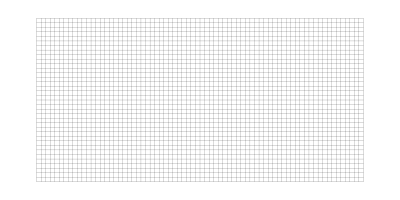

```mathematica
gr1
```

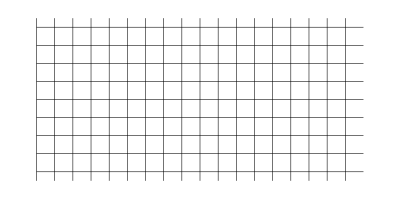

```mathematica
gr0
```

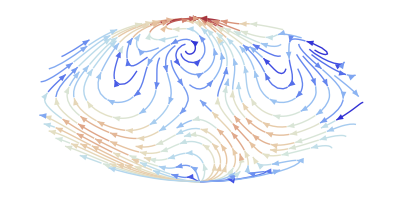

```mathematica
gr2
```

```mathematica
img
```

-Graphics-

```mathematica
(* put it all together *)
```

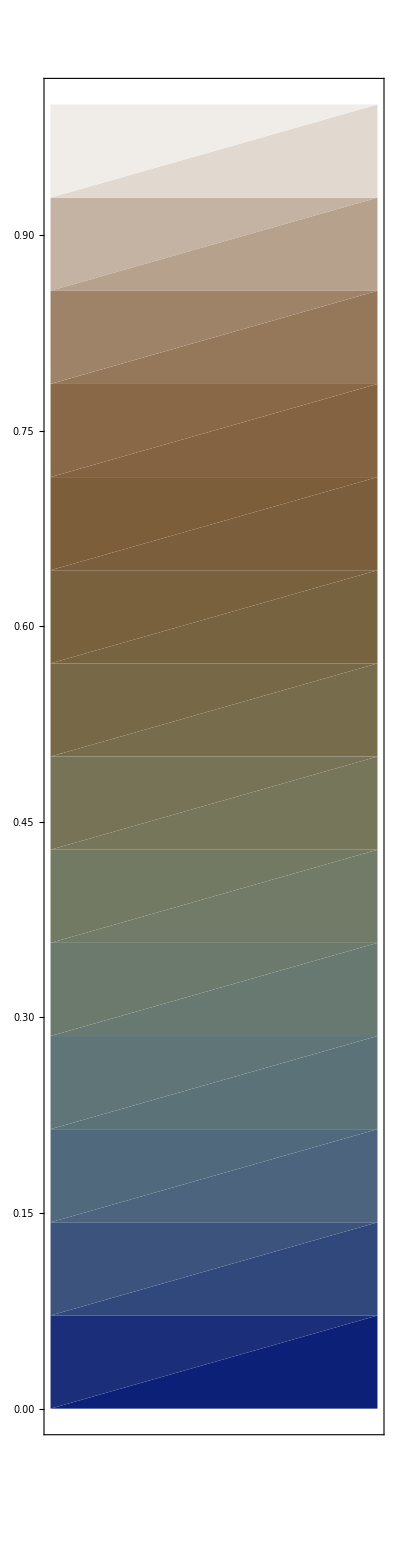
The earth with some crazy vector field
-Graphics-
-Graphics-

```mathematica
Column[{Style["The earth with some crazy vector field",16],Graphics[{Inset[img,{-2,-1},{0,0},{4,2}],First[grid],First[gr2]},PlotRange->{{-2,2},{-1,1}},ImageSize->800],Magnify[Rotate[colorbar[img//ImageData//{Min[#],Max[#]}&,"DarkTerrain"],-90 Degree],1]},Center]
```